```mathematica
Ratesfunc[x_] :=(
ts=x[[1]];
M=x[[2]];
B0=x[[3]];
Em=x[[4]];
Emprime=x[[5]];
η=x[[6]];
λ0=x[[7]];
γ=x[[8]];
ζ=x[[9]];
f0=x[[10]];
mm0=x[[11]];
ef=x[[12]];
χ=x[[13]];

a = B0/Em;
aprime =  B0/Emprime;
ϵLam = 0.25;
m0 = 0.001;
ϵSig = (1-f0*M^γ/M);
ϵMu = (1-(f0*M^γ+mm0*M^ζ)/M);
τLam = -Log[(1-ϵLam^(1/4))/(1 - (m0/M)^(1/4))]*(4*M^(1/4))/a;
τRho = -Log[(1-ϵLam^(1/4))/(1-(ϵSig*ϵLam)^(1/4))]*(4*M^(1/4))/aprime;
τSig = -M^(1/4)/aprime*Log[ϵSig(**ϵLam*)];
τMu = -M^(1/4)/aprime*Log[ϵMu(**ϵLam*)] -τSig;
Growth = ts*(Log[2]/τLam);
Starvation = ts*(1/τSig);
Mortality=ts*( 1/τMu);
Recovery = ts*(1/τRho);
Maintenance = ts*ef*B0*M^η;
Resourcegrowth = ts*0.5;

(*INVADERS*)

{Growth,Starvation,Mortality,Recovery,Maintenance,Resourcegrowth(*,InvaderStarvation,InvaderRecovery,InvaderMaintenance*)}
);
```

```mathematica
parameters={
(*ts*)1,
(*M*)Mass =M,
(*B0*)4.7*10^(-2),
(*Em*)5774(*J/gram*),
(*Emprime*)7000 (*10000*),
(*η*)3/4,
(*λ0*)3.39*10^(-7),
(*γ*)1.19,
(*ζ*)1.00,
(*f0*)0.0202,
(*mm0*)0.383,
(*ef*)0.001,
(*χ*)chi};
RF =Ratesfunc[parameters];
(*GrowthOverM=RF[[1]];
StarvationOverM=RF[[2]];
MortalityOverM = RF[[3]];
RecoveryOverM=RF[[4]];
MaintenanceOverM = RF[[5]];
ResourcegrowthOverM=RF[[6]];*)
```

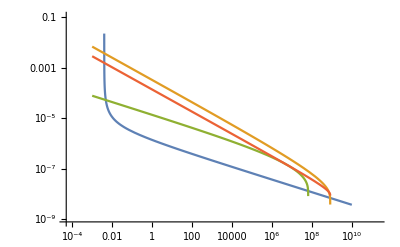

```mathematica
LogLogPlot[{
Growth,
Starvation,
Mortality,
Recovery},{M,0.001,10^10}]
```

```mathematica
Growth/.M->0.002
```

-0.00001093

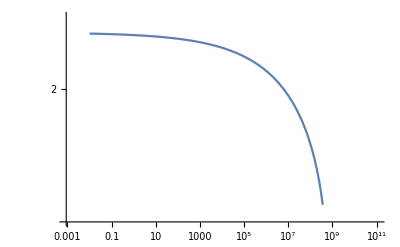

```mathematica
LogLogPlot[Starvation/Recovery,{M,0.01,10^10}]
```